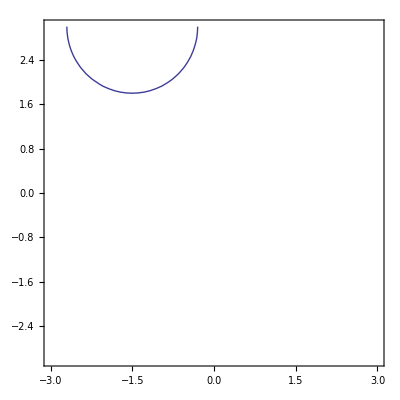

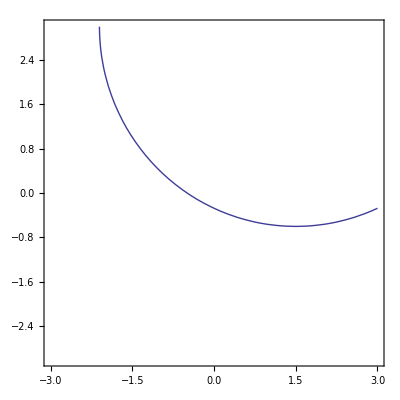

```mathematica
xs=-1.5;
ys=3;
zs=1.5;
n=1.6;
(*Prima faccia*)
z0=3;
ContourPlot[(x-xs)^2*((1/n)^2-1)+(y-ys)^2*((1/n)^2-1)+(1/n^2)*(z0-zs)^2==0,{x,
-3,3},{y,-3,3}]
(*Seconda faccia*)
x0=3;
ContourPlot[(z-zs)^2*((1/n)^2-1)+(y-ys)^2*((1/n)^2-1)+(1/n^2)*(x0-xs)^2==0,{z,
-3,3},{y,-3,3}]
```